## Example 1: Function R -> R

```mathematica
f[a_]:=a^2
```

```mathematica
Df[x_,h_]:=D[(x+alpha h)^2,alpha]/.alpha->0
```

```mathematica
Df[x,h]
Df[1,h]
Df[2,h]
```

2 h x

2 h

4 h

```mathematica
(* h is arbitrary -->>> choose x*)
Df[1,x]
Df[2,x]
```

2 x

4 x

```mathematica
(* Linear approximation *)
```

```mathematica
fw[a0_]:=f[a0]+Df[a0,x-a0]
```

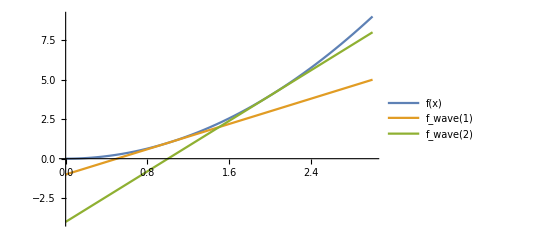

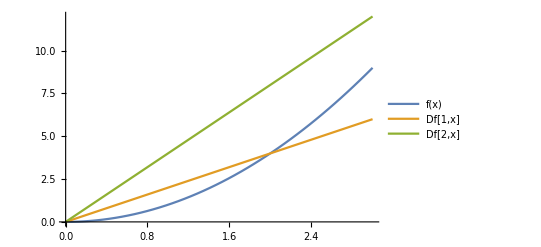

```mathematica
fw1=fw[1];
fw2=fw[2];
p1=Plot[{f[x],fw1,fw2},{x,0,3},PlotLegends->{"f(x)","f_wave(1)","f_wave(2)"},PlotRange->All]
p2=Plot[{f[x],Df[1,x],Df[2,x]},{x,0,3},PlotLegends->{"f(x)","Df[1,x]","Df[2,x]"},PlotRange->All]
```

```mathematica
ClearAll
```

ClearAll

## Example 2: Function R^2 -> R

```mathematica
g[x1_,x2_]:=-x1^2 - x2^2
p={1,1};
```

```mathematica
Dg[x1_,x2_,h1_,h2_]:=D[g[x1+alpha h1,x2+alpha h2],alpha]/.alpha->0//Simplify
```

```mathematica
(* Linear approximation *)
```

```mathematica
gw[a1_,a2_]:=g[a1,a2]+Dg[a1,a2,x1-a1,x2-a2]//Simplify
```

```mathematica
Plot3D[{gw[1,1],g[x1,x2]},{x1,0,3},{x2,0,3}]
```

-Graphics3D-

## Example 3: A functional

```mathematica
phi[u_]:=Integrate[Sqrt[1+(D[u,x])^2],{x,0,1}]
f[x_]:=x;
g[x_]:=x^2;
```

```mathematica
phi[f[x]]
phi[g[x]]
```

√2

1/4 (2 √5+ArcSinh[2])

```mathematica
Dphi[u_,h_]:=D[phi[u+alpha h],alpha]/.alpha->0//Simplify
```

```mathematica
k[0]=0;
k[1]=0;
k'[x]=k[1]-k[0];
```

```mathematica
DphiF=Dphi[f[x],k[x]]//Simplify
```

0

```mathematica
r[x_]:=x;
```

```mathematica
DphiG=Dphi[g[x],r[x]]//Simplify
```

1/2 (-1+√5)

## Example 4: An important class of functionals

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
VariationalD[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
EulerEquations[√(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
DSolve[%,y[x],x]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
ClearAll
```

ClearAll

## Task 1

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
VariationalD[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
g[x1_,x2_]:={x2,Sin[x1+x2],x1^2+x2^2}
```

```mathematica
DG[x1_,x2_,h1_,h2_]:=D[g[x1+alpha h1, x2+ alpha h2],alpha]/.alpha->0
```

```mathematica
DG[x1,x2,h1,h2]//MatrixForm
```

(h2
(h1+h2) Cos[x1+x2]
2 h1 x1+2 h2 x2)

```mathematica
(* ({{h2}, {(h1+h2) Cos[x1+x2]}, {2 h1 x1+2 h2 x2}}) = ({{0 h1 + h2}, {h1 Cos[x1+x2] + h2 Cos[x1+x2]}, {2 h1 x1+2 h2 x2}}) = ({{0, 1}, {Cos(Subscript[x, 1]+Subscript[x, 2]), Cos(Subscript[x, 1]+Subscript[x, 2])}, {2*Subscript[x, 1], 2*Subscript[x, 2]}}).({{Subscript[h, 1]}, {Subscript[h, 2]}}) 
J= ({{0, 1}, {Cos(Subscript[x, 1]+Subscript[x, 2]), Cos(Subscript[x, 1]+Subscript[x, 2])}, {2*Subscript[x, 1], 2*Subscript[x, 2]}}) *)
```

## Task 2

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Clear[p]
```

```mathematica
phi[u_]:=Integrate[EA D[u,x]^2 /2 - p u,{x,0,l}] dx
```

```mathematica
VariationalD[EA D[u[x],x]^2 /2 - p u[x],u[x],x]
```

-p-EA u''[x]

```mathematica
EulerEquations[EA D[u[x],x]^2 /2 - p u[x],u[x],x]
```

-p-EA u''[x]==0

```mathematica
DSolve[%,u[x],x]
```

{{u[x]→-(p x^2)/(2 EA)+C[1]+x C[2]}}

```mathematica
(* phi[u]=∫_0^l (1/2 EA u'^2 - p u)ⅆx
=> Dphi(u)(h)=Lim d/dx∫_0^l (1/2 EA (u'+ alpha h')^2 - p (u+ alpha h))ⅆx
= Lim{ ∫_0^l d/dx(1/2 EA (u'+ alpha h')^2 - p (u+ alpha h))ⅆx }
= Lim{ ∫_0^l ∂/(∂u)[1/2 EA (u'+ alpha h')^2 - p (u+ alpha h)]h
+∂/(∂u')[1/2 EA (u'+ alpha h')^2 - p (u+ alpha h)]h' ⅆx };
		= ∫_0^l { ∂/(∂u)[1/2 EA (u')^2 - p u]h + ∂/(∂u')[1/2 EA (u')^2 - p u]h' }ⅆx 
		= ∫_0^l {∂/(∂u)[1/2 EA (u')^2 - p u]h - d/dx∂/(∂u')[1/2 EA (u')^2 - p u]h}ⅆx 
			+[∂/(∂u')[1/2 EA (u')^2 - p u]]_0^l
		=∫_0^l {∂/(∂u)[1/2 EA (u')^2 - p u] - d/dx∂/(∂u')[1/2 EA (u')^2 - p u]}hⅆx 
			+[∂/(∂u')[1/2 EA (u')^2 - p u]]_0^l
==>>> ∂/(∂u)[1/2 EA (u')^2 - p u] - d/dx∂/(∂u')[1/2 EA (u')^2 - p u] ==0
			=> - p - EA u'' =0
```